```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
udata=ReadList["Geff.dat", {Number,Number}];
cdatah=ReadList["cdatah.txt",{Number,Number}];
```

```mathematica
rudata=Join[udata,cdatah];
```

```mathematica
u=Interpolation[rudata];
ru[r_]:=Piecewise[{{1,0≤r<0.01},{u[r],0.01<=r≤201.5},{1,r>201.5}}];
```

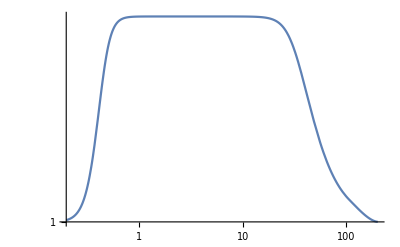

```mathematica
LogLogPlot[ru[r],{r,0,201.5}]
```

```mathematica
du=D[u[r],r];
rdu[r_]:=Piecewise[{{0,0≤r<0.01},{du,0.01<=r≤201.5},{0,r>201.5}}]
```

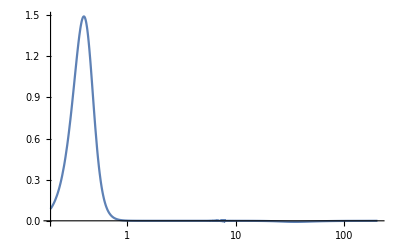

```mathematica
LogLinearPlot[rdu[r],{r,0,201.5},PlotRange->All]
```

```mathematica
(*rdudata=Table[{x,rdu[x]},{x,0,1,0.01}];
rduf=Interpolation[rdudata];
rrduf[r_]:=Piecewise[{{rduf[r],0<=r≤1},{0,r>1}}]*)
```

```mathematica
(*LogLinearPlot[rrduf[r],{r,0,201.5},PlotRange->All]*)
```

```mathematica
rg[r_]:=1;
(*r01=0.01;alpha2=1;beta2=1;alpha1=1.1;beta1=1.1;
 pmu[r_]:=(1+alpha1*(r/r01)^2)/(1+alpha2*(r/r01)^2);
pgamma[r_]:=(1+beta1*(r/r01)^2)/(1+beta2*(r/r01)^2);
Sigma[r_]:=((1+pgamma[r])*pmu[r])/2;*)
```

```mathematica
r01=0.01;
```

```mathematica
Sigma[r_]:=(1+alpha1*(r/r01)^2)/(1+alpha2*(r/r01)^2);
```

```mathematica
r1=0.06;
```

```mathematica
Sigma[r_]:=1+0.05(1+Tanh[20(r-r1)]);
```

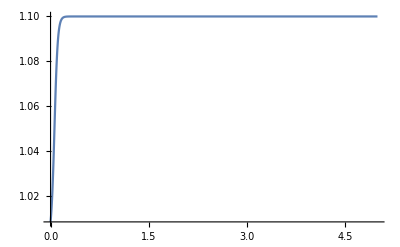

```mathematica
Plot[Sigma[r],{r,0,5},PlotRange->All]
```

```mathematica
Sigma[0.]
```

1.00832

```mathematica
dSigma[r_]:=D[Sigma[a],a]/.a->r
```

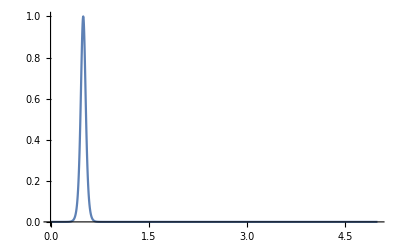

```mathematica
Plot[dSigma[r],{r,0,5},PlotRange->All]
```

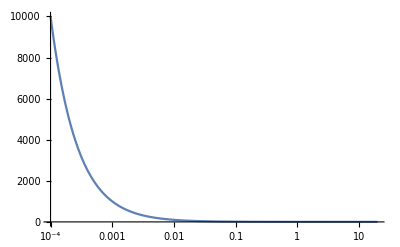

```mathematica
a1[b_]:=b*NIntegrate[Sigma[r]/r^3/.r->√(b^2+z^2),{z,0,∞}]
LogLinearPlot[a1[b],{b,0.0001,20},PlotRange->All]
```

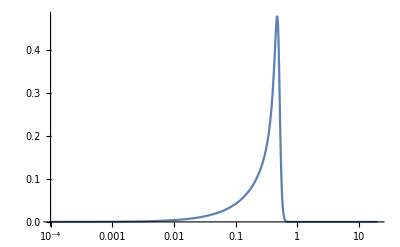

```mathematica
a2[b_]:=b*NIntegrate[dSigma[r]/r^2/.r->√(b^2+z^2),{z,0,Infinity}]
LogLinearPlot[a2[b],{b,0.0001,20},PlotRange->All]
```

```mathematica
(*a3[b_]:=b*NIntegrate[(ru[r]*rdu[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}]
LogLinearPlot[a3[b],{b,0.0001,201.5},PlotRange->All]*)
```

```mathematica
Ib[b_]:=a1[b]-a2[b];
```

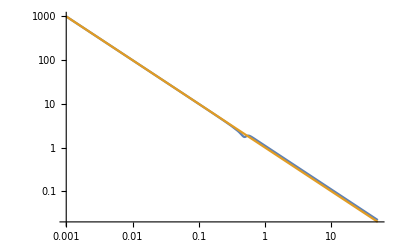

```mathematica
LogLogPlot[{Ib[b],1/b},{b,0.001,50}]
```

```mathematica
Ibdata1=Table[{b,a1[b]-a2[b]},{b,0.001,1,0.001}];
Ibdata2=Table[{b,a1[b]-a2[b]},{b,1.01,50,0.01}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.9387}. NIntegrate obtained 4.4721448290557933337486005496247824183210713930433795181659393598×10^-319 and 4.6797776363876105174886825588150706623944697247899615869766648435×10^-325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.90863}. NIntegrate obtained 2.99537222017116×10^-319 and 4.61859234325482×10^-325 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.55575}. NIntegrate obtained 2.00624376195258×10^-319 and 5.07524872104053×10^-325 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
Ibdata3=Table[{b,a1[b]-a2[b]},{b,0.00101,0.00199,0.00001}];
```

```mathematica
Ibdatan=Join[Ibdata1,Ibdata2,Ibdata3];
```

```mathematica
Ibdata=Sort[Ibdatan,#1[[1]]<#2[[1]]&];
```

```mathematica
Export["Ibdata.txt",Ibdata,"Table"];
```

```mathematica
(*Ibdata=ReadList["Ibdata.txt",{Number,Number}];*)
```

```mathematica
rIb=Interpolation[Ibdata];
```

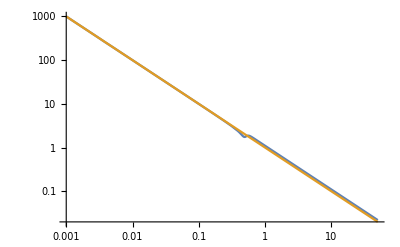

```mathematica
rrIb[b_]:=Piecewise[{{-rIb[-b],-50≤b≤-0.001},{1/b,-0.001<b<0.001},{rIb[b],0.001<=b≤50}}];
LogLogPlot[{rrIb[b],1/b},{b,0.001,50},PlotRange->All]
```

```mathematica
(*LogLogPlot[{a1[b]-a2[b]-a3[b],rrIb[b]},{b,0.01,110},PlotRange->All]*)
```

```mathematica
(*LogLogPlot[{rrIb[b],2/b},{b,0.001,201.5},PlotRange->All]*)
```

```mathematica
(*Itbdata=Table[{Ibdata[[i,1]],Ibdata[[i,2]]/Ibdata[[i,1]]},{i,1,Length[Ibdata]}];*)
```

```mathematica
(*Export["Itbdata.txt",Itbdata,"Table"];*)
```

```mathematica
(*Itbdata=ReadList["Itbdata.txt",{Number,Number}];*)
```

```mathematica
(*rItb=Interpolation[Itbdata];*)
```

```mathematica
(*rrItb[b_]:=Piecewise[{{2/b^2,b<-201.5},{rItb[-b],-201.5≤b≤-0.001},{2/b^2,-0.001<b<0.001},{rItb[b],0.001<=b≤201.5},{2/b^2,b>201.5}}];
LogLogPlot[rrItb[b],{b,0.001,201.5},PlotRange->All]*)
```

```mathematica
(*LogLogPlot[{rrItb[b],2/b^2},{b,0.001,201.5},PlotRange->All]*)
```

```mathematica
zl=0.3;
zs=1;
om=0.3;
h0=70;(*km s^-1 Mpc^-1*)
h0c=68;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^12;(*Msun*)
```

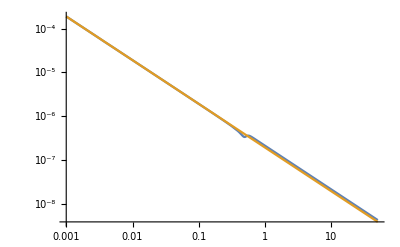

```mathematica
LogLogPlot[{(4G*M)/c^2*1/(30.85678*10^18)*rrIb[b],(4G*M)/c^2*1/(30.85678*10^18)*1/b},{b,0.001,50},PlotRange->All]
```

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DAc[z_]:=c/h0c 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
DA2c[z1_,z2_]:=c/h0c 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];

DA[zl]
DA[zs]
DA2[zl,zs]
DA2[zl,zs]/(DA[zl]*DA[zs])

DAc[zl]
DAc[zs]
DA2c[zl,zs]
DA2c[zl,zs]/(DAc[zl]*DAc[zs])
```

919.403

1653.06

1055.45

0.000694452

946.444

1701.68

1086.49

0.00067461

```mathematica
thetaE=√((4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs]))
thetaEc=√((4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zl]*DAc[zs]))
thetaE*DA[zl]
```

0.0000115224

0.0000113566

0.0105937

```mathematica
n=2000;
```

```mathematica
thetaGRpd=Table[0,{n}];
thetaGRmd=Table[0,{n}];
thetaGRcpd=Table[0,{n}];
thetaGRcmd=Table[0,{n}];
thetaMGpd=Table[0,{n}];
thetaMGmd=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,If[i≤500,y=0.001*(i-1),y=0.5+0.003*(i-501)];thetaGR=theta/.NSolve[theta-y*thetaE==(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zs]DA[zl])*1/theta,theta];thetaGRc=theta/.NSolve[theta-y*thetaE==(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zs]DAc[zl])*1/theta,theta];
thetaGRp=thetaGR[[1]];
thetaGRm=thetaGR[[2]];
thetaGRpd[[i]]={y,thetaGRp};
thetaGRmd[[i]]={y,thetaGRm};
thetaGRcp=thetaGRc[[1]];
thetaGRcm=thetaGRc[[2]];
thetaGRcpd[[i]]={y,thetaGRcp};
thetaGRcmd[[i]]={y,thetaGRcm};
thetaMGp=theta/.FindRoot[theta-y*thetaE==DA2[zl,zs]/DA[zs]*(4G*M)/c^2*1/(30.85678*10^18)*rrIb[DA[zl]*theta],{theta,thetaGRp}];
thetaMGm=theta/.FindRoot[theta-y*thetaE==DA2[zl,zs]/DA[zs]*(4G*M)/c^2*1/(30.85678*10^18)*rrIb[DA[zl]*theta],{theta,thetaGRm}];
thetaMGpd[[i]]={y,thetaMGp};
thetaMGmd[[i]]={y,thetaMGm};]
```

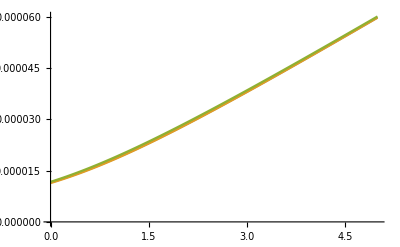

```mathematica
ListPlot[{thetaGRpd,thetaGRcpd,thetaMGpd},Joined->True,PlotRange->All]
```

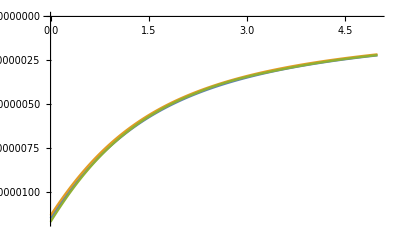

```mathematica
ListPlot[{thetaGRmd,thetaGRcmd,thetaMGmd},Joined->True,PlotRange->All]
```

```mathematica
thetaGRpd=ReadList["thetaGRpd.txt",{Number,Number}];
thetaGRmd=ReadList["thetaGRmd.txt",{Number,Number}];
thetaGRcpd=ReadList["thetaGRcpd.txt",{Number,Number}];
thetaGRcmd=ReadList["thetaGRcmd.txt",{Number,Number}];
thetaMGpd=ReadList["thetaMGpd.txt",{Number,Number}];
thetaMGmd=ReadList["thetaMGmd.txt",{Number,Number}];
```

```mathematica
min1=Min[Table[thetaMGpd[[i,2]],{i,1,n}]]
```

0.000311635

```mathematica
max1=Max[Table[thetaMGpd[[i,2]],{i,1,n}]]
```

0.00192792

```mathematica
min2=Min[Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-0.000311635

```mathematica
max2=Max[Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-0.0000696594

```mathematica
xmin=Min[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

0.0000696594

```mathematica
xmax=Max[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

0.00192792

```mathematica
phihGR[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])Log[Abs[x]];
phihGRc[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zl]*DAc[zs])Log[Abs[x]];
phihMGini[x_]:=NIntegrate[DA2[zl,zs]/DA[zs]*(4*G*M)/c^2*1/(30.85678*10^18)*rrIb[b]/.b->(DA[zl]*theta),{theta,xmin,x}];
phihMG[x_]:=phihMGini[Abs[x]];
```

```mathematica
TDGR=Table[0,{n}];
TDGRc=Table[0,{n}];
TDMG=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,thetaGRp=thetaGRpd[[i,2]];y=thetaGRpd[[i,1]];thetaGRm=thetaGRmd[[i,2]];
alphaGRp=thetaGRp-y*thetaE;
alphaGRm=thetaGRm-y*thetaE;
DettGR=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2(alphaGRm)^2-1/2(alphaGRp)^2-(phihGR[thetaGRm]-phihGR[thetaGRp]));
TDGR[[i]]={y,DettGR};

thetaGRcp=thetaGRcpd[[i,2]];y=thetaGRcpd[[i,1]];thetaGRcm=thetaGRcmd[[i,2]];
alphaGRcp=thetaGRcp-y*thetaE;
alphaGRcm=thetaGRcm-y*thetaE;
DettGRc=(1+zl)/c*30.85678*10^18*(DAc[zl]*DAc[zs])/DA2c[zl,zs](1/2(alphaGRcm)^2-1/2(alphaGRcp)^2-(phihGRc[thetaGRcm]-phihGRc[thetaGRcp]));
TDGRc[[i]]={y,DettGRc};
thetaMGp=thetaMGpd[[i,2]];y=thetaMGpd[[i,1]];thetaMGm=thetaMGmd[[i,2]];
alphaMGp=thetaMGp-y*thetaE;
alphaMGm=thetaMGm-y*thetaE;
DettMG=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2 alphaMGm^2-1/2 alphaMGp^2-(phihMG[thetaMGm]-phihMG[thetaMGp]));
TDMG[[i]]={y,DettMG};]
```

```mathematica
(*TDMG=ReadList["TDMG.txt",{Number,Number}];*)
```

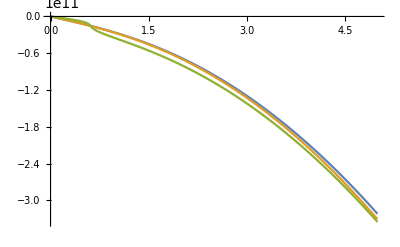

```mathematica
ListPlot[{TDGR,TDGRc,TDMG},Joined->True,PlotRange->All]
```

```mathematica
diffhc=Table[{TDGR[[i,1]],(TDGRc[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
diffMG=Table[{TDGR[[i,1]],(TDMG[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
(*diffMGc=Table[{TDGRt[[i,1]],(TDMGt[[i,2]]-TDGRct[[i,2]])},{i,1,Length[TDMGt]}];*)
```

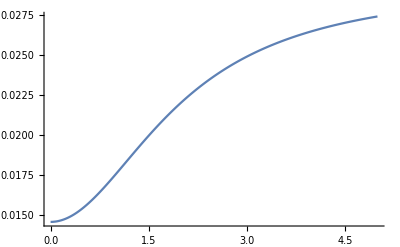

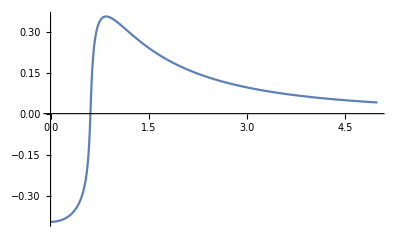

```mathematica
ListLinePlot[diffhc]
ListLinePlot[diffMG]
(*ListLinePlot[diffMGc]*)
```

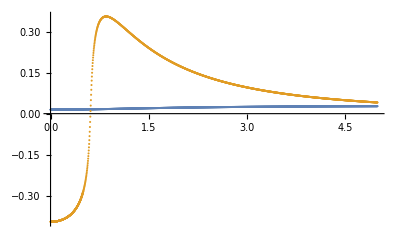

```mathematica
ListPlot[{diffhc,diffMG},PlotRange->All]
```

```mathematica
Export["thetaGRpd.txt",thetaGRpd,"Table"];
Export["thetaGRcpd.txt",thetaGRcpd,"Table"];
Export["thetaMGpd.txt",thetaMGpd,"Table"];
Export["thetaGRmd.txt",thetaGRmd,"Table"];
Export["thetaGRcmd.txt",thetaGRcmd,"Table"];
Export["thetaMGmd.txt",thetaMGmd,"Table"];
```

```mathematica
Export["TDGR.txt",TDGR,"Table"];
Export["TDGRc.txt",TDGRc,"Table"];
Export["TDMG.txt",TDMG,"Table"];
```